### Definitions

```mathematica
Np =4;
d = 1;
lm = 1;
lp[k_]:=((k+1)^(1/4))/lm;
$Assumptions = -1<k && Im[k]==0
xcoord={x1,x2,x3}
xpcoord = {x1p,x2p,x3p}
A[lp_]:=1/(2 lp^2);
B[lm_,lp_, Np_]:=-1/(2Np) (1/lm^2-1/lp^2);
```

-1<k&&Im[k]==0

{x1,x2,x3}

{x1p,x2p,x3p}

### Coefficients from Analytical Calculation

```mathematica
p00int[a_, b_] := -6((a^2 (-4 a^4+32 a^3 b-93 a^2 b^2+116 a b^3-54 b^4))/(12 √(a-3 b) √((a (a-2 b))/(a-b)) (a-b)^(5/2) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a))))
p11int[a_,b_]:=6*(a^2 (16 a^8-256 a^7 b+1724 a^6 b^2-6352 a^5 b^3+13957 a^4 b^4-18728 a^3 b^5+15096 a^2 b^6-6816 a b^7+1464 b^8))/(48 (a-3 b)^(5/2) √((a (a-2 b))/(a-b)) (a-b)^(9/2) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))


p22int[a_,b_]:=6*-((a^2 b^2 (-256 a^10+5120 a^9 b-44452 a^8 b^2+219712 a^7 b^3-682541 a^6 b^4+1391644 a^5 b^5-1892622 a^4 b^6+1708080 a^3 b^7-988824 a^2 b^8+340704 a b^9-66960 b^10))/(768 (a-3 b)^(9/2) √((a (a-2 b))/(a-b)) (a-b)^(13/2) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a))))
p33int[a_,b_]:=6*(a^2 b^4 (1296 a^12-31104 a^11 b+333628 a^10 b^2-2110640 a^9 b^3+8752725 a^8 b^4-25011024 a^7 b^5+50403416 a^6 b^6-72161952 a^5 b^7+73108400 a^4 b^8-51519360 a^3 b^9+24170688 a^2 b^10-7026432 a b^11+1315584 b^12))/(3072 (a-3 b)^(13/2) √((a (a-2 b))/(a-b)) (a-b)^(17/2) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
p44int[a_,b_]:=6*(5 a^2 b^6 (20480 a^14-573440 a^13 b+7381780 a^12 b^2-57887200 a^11 b^3+308419825 a^10 b^4-1177022420 a^9 b^5+3301650254 a^8 b^6-6876931424 a^7 b^7+10638473440 a^6 b^8-12145693056 a^5 b^9+10110024960 a^4 b^10-5995573248 a^3 b^11+2412418176 a^2 b^12-616960512 a b^13+106801920 b^14))/(196608 (a-3 b)^(17/2) √((a (a-2 b))/(a-b)) (a-b)^(21/2) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

p55int[a_,b_]:=6*(7 √((a (a-2 b))/(a-b)) b^8 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (70000 a^16-2240000 a^15 b+33815908 a^14 b^2-319645424 a^13 b^3+2111381251 a^12 b^4-10278421832 a^11 b^5+37878905848 a^10 b^6-106980595232 a^9 b^7+232326714856 a^8 b^8-386927766144 a^7 b^9+490757682048 a^6 b^10-469089172992 a^5 b^11+332847093888 a^4 b^12-170781041664 a^3 b^13+60226845696 a^2 b^14-13765496832 a b^15+2162654208 b^16))/(786432 a^2 (a-3 b)^(23/2) (a-b)^(25/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
p66int[a_,b_]:=6*(7 √((a (a-2 b))/(a-b)) b^10 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (435456 a^18-15676416 a^17 b+272391924 a^16 b^2-3031228032 a^15 b^3+24078957777 a^14 b^4-143844526812 a^13 b^5+663857700870 a^12 b^6-2399943912912 a^11 b^7+6838907811192 a^10 b^8-15379009683168 a^9 b^9+27214669306128 a^8 b^10-37664153038080 a^7 b^11+40395367337088 a^6 b^12-33170049965568 a^5 b^13+20502998081792 a^4 b^14-9271265486848 a^3 b^15+2913360638976 a^2 b^16-603288211456 a b^17+86108657664 b^18))/(4194304 a^2 (a-3 b)^(27/2) (a-b)^(29/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
p77int[a_,b_]:=(11 a^2 b^12 (1267728 a^20-50709120 a^19 b+998794236 a^18 b^2-12833233776 a^17 b^3+119607983253 a^16 b^4-850483633824 a^15 b^5+4738548188616 a^14 b^6-21001211445984 a^13 b^7+74676898669296 a^12 b^8-213949274546304 a^11 b^9+494270740852416 a^10 b^10-918686229652224 a^9 b^11+1366757733444736 a^8 b^12-1614859880310784 a^7 b^13+1499572077065216 a^6 b^14-1079907836342272 a^5 b^15+592041296398336 a^4 b^16-239700850196480 a^3 b^17+68091055644672 a^2 b^18-12929219592192 a b^19+1687516692480 b^20))/(16777216 (a-3 b)^(29/2) √((a (a-2 b))/(a-b)) (a-b)^(33/2) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
p88int[a_,b_]:=0.0001*a
```

```mathematica
p0upi[a_,b_]:=(4 √a (2 a^2-8 a b+5 b^2))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2) √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
p1upi[a_,b_]:=(4 √a (8 a^4-64 a^3 b+152 a^2 b^2-96 a b^3+31 b^4))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^2 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
p2upi[a_,b_]:=(36 √a b^2 (4 a^4-32 a^3 b+72 a^2 b^2-32 a b^3+13 b^4))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^3 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
p3upi[a_,b_]:=(12 √a b^2 (16 a^6-192 a^5 b+904 a^4 b^2-2112 a^3 b^3+2370 a^2 b^4-776 a b^5+245 b^6))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^4 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
p4upi[a_,b_]:=(12 √a b^4 (164 a^6-1968 a^5 b+8898 a^4 b^2-18704 a^3 b^3+17634 a^2 b^4-4872 a b^5+1463 b^6))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^5 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
p5upi[a_,b_]:=(12 √a b^4 (80 a^8-1280 a^7 b+9520 a^6 b^2-42560 a^5 b^3+116990 a^4 b^4-183280 a^3 b^5+139412 a^2 b^6-33488 a b^7+9205 b^8))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^6 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
p6upi[a_,b_]:=(4 √a b^6 (3880 a^8-62080 a^7 b+425680 a^6 b^2-1631680 a^5 b^3+3736174 a^4 b^4-4919152 a^3 b^5+3201436 a^2 b^6-690928 a b^7+176533 b^8))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^7 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
p7upi[a_,b_]:=(4 √a b^6 (1120 a^10-22400 a^9 b+231280 a^8 b^2-1550080 a^7 b^3+6922300 a^6 b^4-20347600 a^5 b^5+38251318 a^4 b^6-42864304 a^3 b^7+24335674 a^2 b^8-4806504 a b^9+1144991 b^10))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^8 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
p8upi[a_,b_]:=(12 √a b^8 (8260 a^10-165200 a^9 b+1521450 a^8 b^2-8484000 a^7 b^3+31194408 a^6 b^4-76851936 a^5 b^5+123734892 a^4 b^6-121063776 a^3 b^7+61119630 a^2 b^8-11204408 a b^9+2500375 b^10))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^9 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
```

```mathematica
p0downi[a_,b_]:=(4 √a (2 a^2-8 a b+5 b^2))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2) √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
p1downi[a_,b_]:=(4 √a (8 a^4-64 a^3 b+152 a^2 b^2-96 a b^3+31 b^4))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^2 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
p2downi[a_,b_]:=(36 √a b^2 (4 a^4-32 a^3 b+72 a^2 b^2-32 a b^3+13 b^4))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^3 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
p3downi[a_,b_]:=(12 √a b^2 (16 a^6-192 a^5 b+904 a^4 b^2-2112 a^3 b^3+2370 a^2 b^4-776 a b^5+245 b^6))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^4 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
p4downi[a_,b_]:=(12 √a b^4 (164 a^6-1968 a^5 b+8898 a^4 b^2-18704 a^3 b^3+17634 a^2 b^4-4872 a b^5+1463 b^6))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^5 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
p5downi[a_,b_]:=(12 √a b^4 (80 a^8-1280 a^7 b+9520 a^6 b^2-42560 a^5 b^3+116990 a^4 b^4-183280 a^3 b^5+139412 a^2 b^6-33488 a b^7+9205 b^8))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^6 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
p6downi[a_,b_]:=(4 √a b^6 (3880 a^8-62080 a^7 b+425680 a^6 b^2-1631680 a^5 b^3+3736174 a^4 b^4-4919152 a^3 b^5+3201436 a^2 b^6-690928 a b^7+176533 b^8))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^7 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
p7downi[a_,b_]:=(4 √a b^6 (1120 a^10-22400 a^9 b+231280 a^8 b^2-1550080 a^7 b^3+6922300 a^6 b^4-20347600 a^5 b^5+38251318 a^4 b^6-42864304 a^3 b^7+24335674 a^2 b^8-4806504 a b^9+1144991 b^10))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^8 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
p8downi[a_,b_]:=(12 √a b^8 (8260 a^10-165200 a^9 b+1521450 a^8 b^2-8484000 a^7 b^3+31194408 a^6 b^4-76851936 a^5 b^5+123734892 a^4 b^6-121063776 a^3 b^7+61119630 a^2 b^8-11204408 a b^9+2500375 b^10))/(√((a-3 b)/(a^2-4 a b)) √((4 a^2-14 a b+3 b^2)/(a-3 b)) (4 a^2-16 a b+7 b^2)^9 √((a (4 a^2-16 a b+7 b^2))/(4 a^2-14 a b+3 b^2)))
```

```mathematica
p0up[k_]:=p0upi[A[lp[k]], B[1,lp[k],Np]]-p00int[A[lp[k]], B[1,lp[k],Np]]
p1up[k_]:=p1upi[A[lp[k]], B[1,lp[k],Np]]-p11int[A[lp[k]], B[1,lp[k],Np]]
p2up[k_]:=p2upi[A[lp[k]], B[1,lp[k],Np]]-p22int[A[lp[k]], B[1,lp[k],Np]]
p3up[k_]:=p3upi[A[lp[k]], B[1,lp[k],Np]]-p33int[A[lp[k]], B[1,lp[k],Np]]
p4up[k_]:=p4upi[A[lp[k]], B[1,lp[k],Np]]-p44int[A[lp[k]], B[1,lp[k],Np]]
p5up[k_]:=p5upi[A[lp[k]], B[1,lp[k],Np]]-p55int[A[lp[k]], B[1,lp[k],Np]]
p6up[k_]:=p6upi[A[lp[k]], B[1,lp[k],Np]]-p66int[A[lp[k]], B[1,lp[k],Np]]
p7up[k_]:=p7upi[A[lp[k]], B[1,lp[k],Np]]-p77int[A[lp[k]], B[1,lp[k],Np]]
p8up[k_]:=p8upi[A[lp[k]], B[1,lp[k],Np]]-p88int[A[lp[k]], B[1,lp[k],Np]]
```

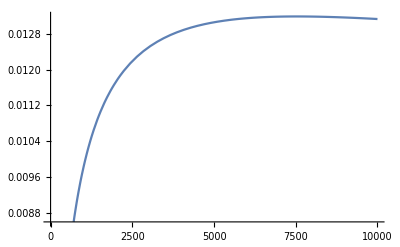

```mathematica
Plot[p66int[A[lp[k]], B[1,lp[k],Np]], {k,-0.99,10000}]
```

```mathematica
p0down[k_]:=p0downi[A[lp[k]], B[1,lp[k],Np]]-p00int[A[lp[k]], B[1,lp[k],Np]]
p1down[k_]:=p1downi[A[lp[k]], B[1,lp[k],Np]]-p11int[A[lp[k]], B[1,lp[k],Np]]
p2down[k_]:=p2downi[A[lp[k]], B[1,lp[k],Np]]-p22int[A[lp[k]], B[1,lp[k],Np]]
p3down[k_]:=p3downi[A[lp[k]], B[1,lp[k],Np]]-p33int[A[lp[k]], B[1,lp[k],Np]]
p4down[k_]:=p4downi[A[lp[k]], B[1,lp[k],Np]]-p44int[A[lp[k]], B[1,lp[k],Np]]
p5down[k_]:=p5downi[A[lp[k]], B[1,lp[k],Np]]-p55int[A[lp[k]], B[1,lp[k],Np]]
p6down[k_]:=p6downi[A[lp[k]], B[1,lp[k],Np]]-p66int[A[lp[k]], B[1,lp[k],Np]]
p7down[k_]:=p7downi[A[lp[k]], B[1,lp[k],Np]]-p77int[A[lp[k]], B[1,lp[k],Np]]
p8down[k_]:=p8downi[A[lp[k]], B[1,lp[k],Np]]-p88int[A[lp[k]], B[1,lp[k],Np]]
```

```mathematica
Plot[p2vac[k], {k,-0.99,10}]
```

-Graphics-

```mathematica
p0updown[k_]:= p00int[A[lp[k]], B[1,lp[k],Np]]
p1updown[k_]:= p11int[A[lp[k]], B[1,lp[k],Np]]
p2updown[k_]:= p22int[A[lp[k]], B[1,lp[k],Np]]
p3updown[k_]:= p33int[A[lp[k]], B[1,lp[k],Np]]
p4updown[k_]:= p44int[A[lp[k]], B[1,lp[k],Np]]
p5updown[k_]:= p55int[A[lp[k]], B[1,lp[k],Np]]
p6updown[k_]:= p66int[A[lp[k]], B[1,lp[k],Np]]
p7updown[k_]:= p77int[A[lp[k]], B[1,lp[k],Np]]
p8updown[k_]:= p88int[A[lp[k]], B[1,lp[k],Np]]

p0vac[k_]:= 1-p0up[k]-p0down[k]-p0updown[k]
p1vac[k_]:= 1-p1up[k]-p1down[k]-p1updown[k]
p2vac[k_]:= 1-p2up[k]-p2down[k]-p2updown[k]
p3vac[k_]:= 1-p3up[k]-p3down[k]-p3updown[k]
p4vac[k_]:= 1-p4up[k]-p4down[k]-p4updown[k]
p5vac[k_]:= 1-p5up[k]-p5down[k]-p5updown[k]
p6vac[k_]:= 1-p6up[k]-p6down[k]-p6updown[k]
p7vac[k_]:= 1-p7up[k]-p7down[k]-p7updown[k]
p8vac[k_]:= 1-p8up[k]-p8down[k]-p8updown[k]
```

## Null

```mathematica
acc = 20
```

20

```mathematica
s[i_]:=If[i==0,0,-i*Log[i]]
logc[i_]:=If[i≤10^(-acc),0,Log[i]]
```

```mathematica
q0[k_] := {p0vac[k], p1vac[k], p2vac[k], p3vac[k], p4vac[k], p5vac[k], p6vac[k], p7vac[k],p8vac[k]}
q1[k_] :={p0up[k], p1up[k], p2up[k], p3up[k], p4up[k], p5up[k], p6up[k],p7up[k], p8up[k]}
q2[k_] :={p0down[k], p1down[k], p2down[k], p3down[k], p4down[k], p5down[k], p6down[k],p7down[k], p8down[k]}
q3[k_] :={p0updown[k], p1updown[k], p2updown[k], p3updown[k], p4updown[k], p5updown[k], p6updown[k],p7updown[k], p8updown[k]}
```

```mathematica
q0[0.9]
```

{6.39471×10^-6,0.00635863,0.992027,0.995165,0.999921,0.999989,1.,1.,1.00004}

```mathematica
(*without SSR*)
e[k_, i_] := s[q0[k][[i+1]]]+s[q1[k][[i+1]]]+s[q2[k][[i+1]]]+s[q3[k][[i+1]]]
i[k_,i_]:= 2*e[k,i]
```

```mathematica
(*with PSSR*)
ip[k_, m_] := 2*e[k,m]-s[(q0[k][[m+1]]+q3[k][[m+1]])] -s[(q1[k][[m+1]]+q2[k][[m+1]])]
ep[k_, m_] := e[k,m]-s[(q1[k][[m+1]]+q2[k][[m+1]])]-s[(q0[k][[m+1]]+q3[k][[m+1]])]
(*with NSSR*)
in[k_, m_] := 2*e[k,m]-s[q0[k][[m+1]]]-s[(q1[k][[m+1]]+q2[k][[m+1]])]-s[q3[k][[m+1]]]
en[k_, m_] := -s[(q1[k][[m+1]]+q2[k][[m+1]])]+s[ q1[k][[m+1]]]+s[q2[k][[m+1]]]
```

```mathematica
export[dataset_,label_]:=Export["/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN4d1_1mode/data_ferm_4d1_mode/"<>ToString[label],dataset, "CSV"]
```

```mathematica
(*export[Flatten[Table[ip[k,2], {k,-0.99,-0.01,0.01}]], ipmode2neg]*)
```

```mathematica
"/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN4d1_1mode/data_ferm_4d1_mode/ipmode2neg"
```

/Users/janoleernst/Desktop/DPhil/Code/GIT-Mode-Entanglement/Analytic Results spinN4d1_1mode/data_ferm_4d1_mode/ipmode2neg

```mathematica
kappalogrange[i_]:= If[i≤0, i, 10^(i-1)]
epeexpneg[i_]:=export[Flatten[Table[ep[k,i]/e[k,i], {k,-0.99,-0.01,0.01}]], "epemode"<>ToString[i]"neg"]
eneexpneg[i_]:=export[Flatten[Table[en[k,i]/e[k,i], {k,-0.99,-0.01,0.01}]], "enemode"<>ToString[i]"neg"]
epeexppos[i_]:=export[Flatten[Table[ep[kappalogrange[k],i]/e[kappalogrange[k],i], {k,0.01,5,0.01}]], "epemode"<>ToString[i]"pos"]
eneexppos[i_]:=export[Flatten[Table[en[kappalogrange[k],i]/e[kappalogrange[k],i], {k,0.01,5,0.01}]], "enemode"<>ToString[i]"pos"]
```

```mathematica
(*Table[epeexpneg[i], {i,0,8}]
Table[eneexpneg[i], {i,0,8}]*)
```

```mathematica
(*Table[epeexppos[i], {i,0,8}]
Table[eneexppos[i], {i,0,8}]*)
```

```mathematica
Plot[(i[j,1]), {j,-0.99,1000000000000},PlotRange->Full]
```

```mathematica
e[1000000000000000000000000000000.23,1]
```

2.819302885020015354253339725345×10^-6

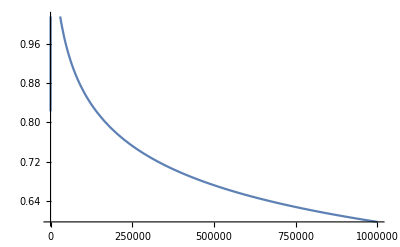

```mathematica
Plot[e[k,1], {k,-0.99,10000000}]
```

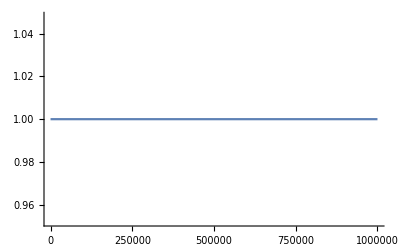

```mathematica
Plot[(e[k,2])/(e[k,2]), {k,-0.99,1000000}]
```

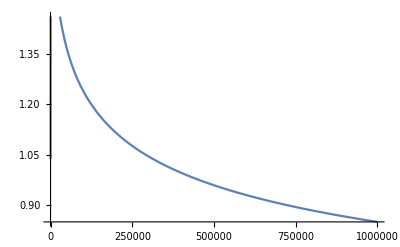

```mathematica
Plot[(i[k,3]), {k,-0.99,1000000}]
```

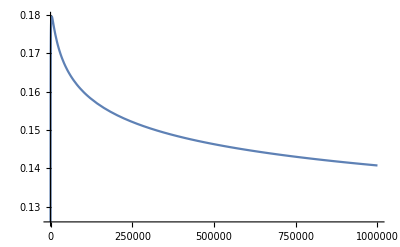

```mathematica
Plot[(en[k,4])/(e[k,4]), {k,-0.99,1000000}]
```

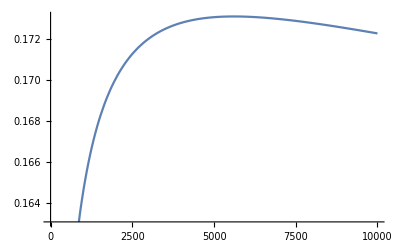

```mathematica
Plot[(en[k,5])/(e[k,5]), {k,-0.99,10000}]
```

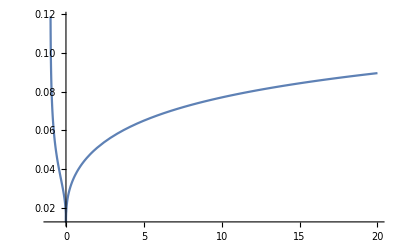

```mathematica
Plot[(en[k,6])/(e[k,6]), {k,-0.99,20}]
```

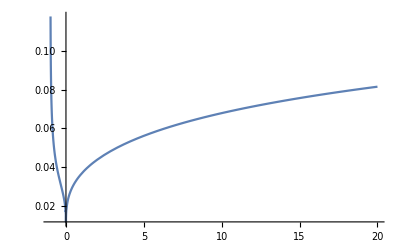

```mathematica
Plot[(en[k,7])/(e[k,7]), {k,-0.99,20}]
```

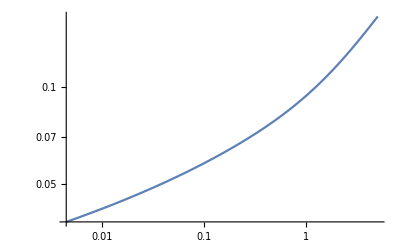

```mathematica
LogLogPlot[(ep[k,0])/(e[k,0]), {k,-0.99,5}]
```

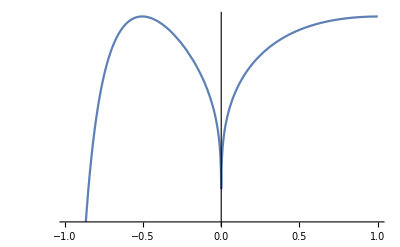

```mathematica
LogPlot[(ep[k,1])/(e[k,1]), {k,-0.99,1}]
```

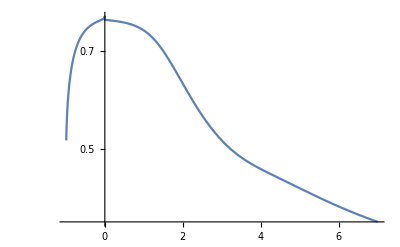

```mathematica
LogPlot[(ep[kappalogrange[k],2])/(e[kappalogrange[k],2]), {k,-0.99,7}]
```

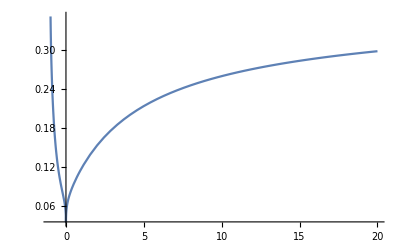

```mathematica
Plot[(ep[k,3])/(e[k,3]), {k,-0.99,20}]
```

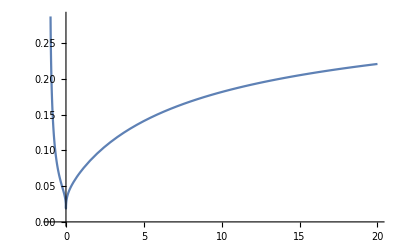

```mathematica
Plot[(ep[k,4])/(e[k,4]), {k,-0.99,20}]
```

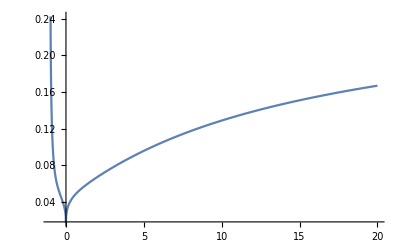

```mathematica
Plot[(ep[k,5])/(e[k,5]), {k,-0.99,20}]
```

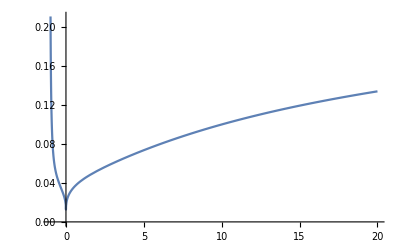

```mathematica
Plot[(ep[k,6])/(e[k,6]), {k,-0.99,20}]
```

```mathematica
ep[0,6]
```

0

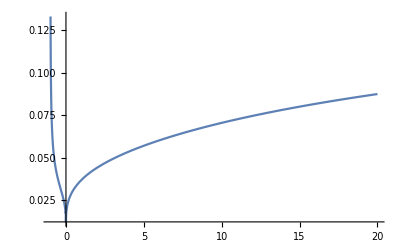

```mathematica
Plot[(ep[k,7])/(e[k,7]), {k,-0.99,20}]
```

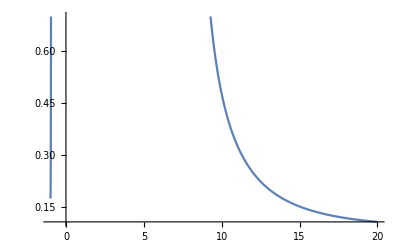

```mathematica
Plot[(ep[k,8])/(e[k,8]), {k,-0.99,20}]
```